### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 2; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-8,8},l];
ker = RandomInteger[{-8,8},td*blocks];
upker = RandomInteger[{-8,8},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

212

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upker]];
```

### After simulation:

```mathematica
ker
```

{-7,0,-13,4,7,3,6,-14}

```mathematica
expected
```

{-182,22,259,89,-6,-400,-192,226,175,-60,-141,-188,103,-33,-120,92,123,156,-289,-407,-380,143,373,15,-32,-20,-146,-41,-19,-104,75,-177,230,112,-312,-253,-209,210,91,12,-136,-243,319,3,291,-237,-95,328,-53,215,-375,-169,61,31,333,138,131,162,-494,-109,10,-17,-6,-122,90,173,-177,97,36,-97,40,-426,211,368,3,39,-224,18,227,-151,250,-225,-21,-137,-218,267,-420,331,-284,312,197,-213,95,-551,229,175,241,224,-546,128}

```mathematica
upker
```

{-12,-3,-5,15,6,-4,16,2,13,-15,-13,-5}

```mathematica
Max[lol]
```

4313

```mathematica
lol=ListConvolve[Reverse[upker],Riffle[expected,0],1,0]
```

{0,140,-280,299,-808,306,-868,766,-1453,731,-1706,1585,-2595,544,-2367,1269,-1301,380,-1117,1342,-1569,-783,466,74,-10,-335,168,622,-43,-641,-449,612,273,-633,334,404,-84,-303,990,-943,675,494,201,-756,140,964,-1439,69,-827,153,572,35,1014,-69,644,-1658,1984,-1297,1947,-801,1352,1002,-366,-673,-477,476,453,-953,870,1195,-353,-724,82,-318,21,-206,364,868,-944,503,-1104,59,-29,-308,-5,507,-54,47,-369,-197,-406,278,19,-688,703,937,282,-956,381,-256,888,-1278,1554,-195,1402,-340,1587,-1819,2807,-1610,4313,-2018,3346,-978,2088,-1741,2385,-708,913,1635,-2002,636,-2699,1885,-3168,1284,-3464,3026,-4141,1231,-3597,1882,-3319,284,-1342,1132,-884,-147,131,-848,2395,-1666,2754,-1771,3295,-1571,3829,-2255,3025,-724,3192,-1972,2719,123,183,-642,450,480,-1350,698,-1279,1744,-1481,-120,-1603,1362,-531,-1898,1136,1242,124,-1118,833,7,253,-1386,1839,12,1480,-605,824,292,79,-1927,1184,1012,-1,336,-1851,2236,-3332,239,-2827,2039,-3087,1973,-3049,1387,-2404}

```mathematica
2^13
```

8192

```mathematica
result
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,140,-280,299,-808,306,-868,766,-1453,731,-1706,1585,-2595,544,-2367,1269,-1301,380,-1117,1342,-1569,-783,466,74,-10,-335,168,622,-43,-641,-449,612,273,-633,334,404,-84,-303,990,-943,675,494,201,-756,140,964,-1439,69,-827,153,572,35,1014,-69,644,-1658,1984,-1297,1947,-801,1352,1002,-366,-673,-477,476,453,-953,870,1195,-353,-724,82,-318,21,-206,364,868,-944,503,-1104,59,-29,-308,-5,507,-54,47,-369,-197,-406,278,19,-688,703,937,282,-956,381,-256,888,-1278,1554,-195,1402,-340,1587,-1819,2807,-1610,4313,-2018,3346,-978,2088,-1741,2385,-708,913,1635,-2002,636,-2699,1885,-3168,1284,-3464,3026,-4141,1231,-3597,1882,-3319,284,-1342,1132,-884,-147,131,-848,2395,-1666,2754,-1771,3295,-1571,3829,-2255,3025,-724,3192,-1972,2719,123,183,-642,450,480,-1350,698,-1279,1744,-1481,-120,-1603,1362,-531,-1898,1136,1242,124,-1118,833,7,253,-1386,1839,12,1480,-605,824,292,79,-1927,1184,1012,-1,336,-1851,2236,-3332,239,-2827,2039,-3087,1973,-3049,1387,-2404,490,-653,-1282,1574,-98,1742,-1822,2492,-925,2813,-1974,2216,56,606,-660,290,533,-595,664,-802,489,-768,222,-384,-144,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{-119}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap10.dat"]];
registers = {"fir_in","sum_loop_out", "sum_loop_end", "count","x","coef_crr","sum_in","sum_out"};
```

```mathematica
firIn=Downsample[snaps[[1]],2,1]; firOut = Downsample[snaps[[2]],2,2];
```

```mathematica
BitShiftRight[firOut,16]
```

{-808,-870,-773,-536,-207,148,459,661,715,609,366,34,-319,-625,-822,-869,-757,-509,-174,179,481,670,708,588,334,-2,-354,-651,-833,-864,-737,-478,-137,214,507,682,705,570,305,-35,-385,-673,-841,-857,-715,-445,-100,248,532,693}

```mathematica
firOutS=Downsample[snaps[[3]],2]
```

{-600,-809,-871,-774,-537,-208,148,459,661,715,609,366,34,-320,-626,-823,-870,-758,-510,-175,179,481,670,708,588,334,-3,-355,-652,-834,-865,-738,-479,-138,214,507,682,705,570,305,-36,-386,-674,-842,-858,-716,-446,-101,248,532}

```mathematica
ker={52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}
```

{52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}

```mathematica
ListConvolve[ker,firIn]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627,45823061,36013029,17970542,-4690099,-27426384,-45682845,-55802274,-55750681,-45520180,-27146941,-4329981,18318687,36221815,45779846}

```mathematica
firOut
```

{-52957126,-57045866,-50703626,-35175093,-13569241,9758538,30096254,43349108,46869436,39968431,24041994,2279233,-20959773,-41020978,-53889101,-56984195,-49673534,-33403820,-11441120,11783828,31578304,43958256,46453047,38580780,21933273,-151579,-23242434,-42710790,-54654944,-56677116,-48354338,-31333836,-9031638,14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

```mathematica
LongestCommonSubsequence[ListConvolve[ker,firIn],firOut]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

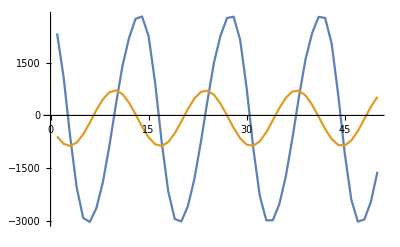

```mathematica
ListPlot[{firIn,firOutS},Joined->True]
```

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

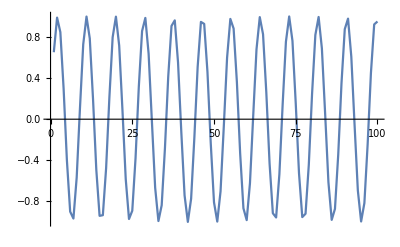

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Riffle[in,0];
```

```mathematica
out=ListConvolve[upker,inR,1,0];
```

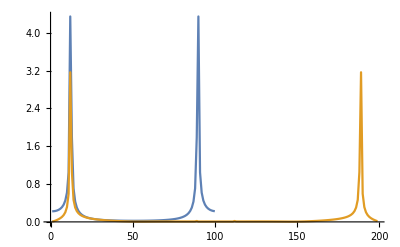

```mathematica
ListPlot[{Abs[Fourier[in]],Abs[Fourier[out]]},Joined->True,PlotRange->All]
```

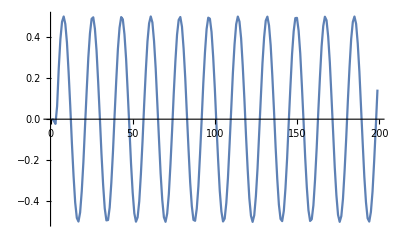

```mathematica
ListPlot[out,Joined->True]
```